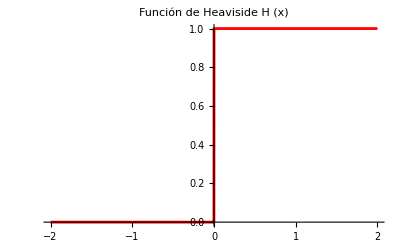

```mathematica
Plot[HeavisideTheta[x],{x,-2,2}, PlotStyle->Red, PlotLabel->Style["Función de Heaviside H (x)", FontSize->16, Black]]
```

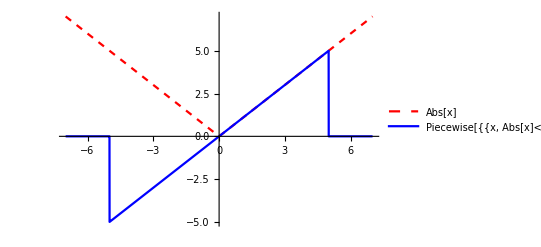

```mathematica
Plot[{Abs[x],Piecewise[{{x,Abs[x]<5},{0,Abs[x]>5}}]},{x,-7,7}, PlotStyle->{{Dashed, Red},{Blue}},ExclusionsStyle->None, PlotLegends->"Expressions"]
```

```mathematica
f[x_]=Piecewise[{{x,Abs[x]<5},{0,Abs[x]>5}}];
TF=FourierTransform[f[x],x,u]//FullSimplify
ReImPlot[TF,{x,-100,100},PlotLegends->Automatic]
```

(√(2/π) (-5 ⅈ u Cos[5 u]+ⅈ Sin[5 u]))/u^2

-Graphics-

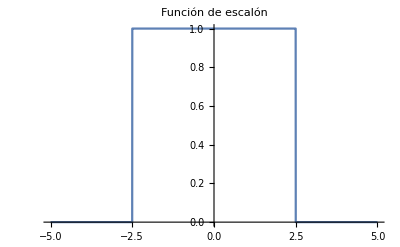

(0.797885 Sin[2.5 u])/u

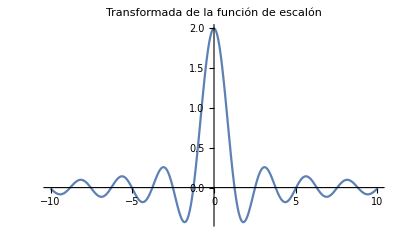

```mathematica
g[x_]=Piecewise[{{1,Abs[x]≤2.5}},0];
Plot[g[x],{x,-5,5}, PlotLabel->Style["Función de escalón", FontSize->16, Black]]
TF=FourierTransform[g[x],x,u]//FullSimplify
Plot[TF,{u,-10,10}, PlotLabel->Style["Transformada de la función de escalón", FontSize->16, Black],PlotRange->All]
```

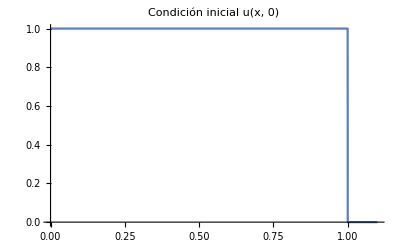

ConditionalExpression[-1/2 x (-2 Erf[1/(2 √t)]+Erf[1/(√t)]), Re[t]>0]

```mathematica
temp[x_]=Piecewise[{{1,0 < x < 1}, {0, x > 1}}];
Plot[temp[x],{x,0,1.1}, PlotLabel->Style["Condición inicial u(x, 0)", FontSize->16,Black]]
u[x_,t_]=2/Pi Integrate[(1-Cos[z])/z Exp[-z^2 t] Sin[z] x,{z,0,∞}]
```

```mathematica
Plot3D[u[x,t],{x,0,1},{t,0,10}, PlotLabel->Style["Distribución de la temperatura u(x,t)", FontSize->16, Black, FontFamily->"Arial"], AxesLabel->{Style[ x,FontSize->20],Style[t,FontSize->20], None}, PlotTheme->"Classic"]
```

-Graphics3D-

```mathematica
h[x_]=1/(√(2 Pi))Integrate[x Exp[ⅈ z x],{x,-5,5}]
Plot[Real[h[x]],{x,-10,10},PlotRange->All]
```

(ⅈ √(2/π) (-5 z Cos[5 z]+Sin[5 z]))/z^2

```mathematica
TrigReduce[(ⅈ √(2/π) (-5 z Cos[5 z]+Sin[5 z]))/z^2]
```

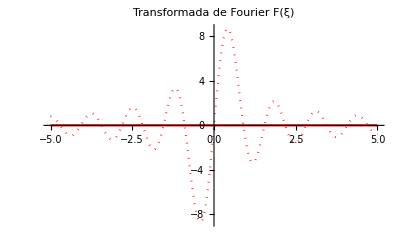

```mathematica
solucion=(ⅈ √(2/π) (-5 z Cos[5 z]+Sin[5 z]))/z^2;
ReImPlot[solucion,{z,-5,5},PlotLabel->Style["Transformada de Fourier F(ξ)", FontSize->16, Black], PlotRange->All, PlotStyle->{Red}]
```